```mathematica
ClearAll
Clear[β3,β4,δ2,γ2,ϵLB, q, S, V,R,n,ϵa,α,r]

W=(((1-q)*β4)/(γ2))*(1-ϵLB*(((1-ϵa)*r)/(α+(1-ϵa)*r))) + ((q*β3)/(γ2+δ2))*(1-ϵLB*(((1-ϵa)*r)/(α+(1-ϵa)*r)))
A=D[W,β3]*(β3/W)
B=D[W,β4]*(β4/W)
F=D[W,δ2]*(δ2/W)
G=D[W,γ2]*(γ2/W)
J=D[W,q]*(q/W)
Ñ=D[W,ϵLB]*(ϵLB/W)
S=D[W,ϵa]*(ϵa/W)
P=D[W,r]*(r/W)
M=D[W,α]*(α/W)
```

ClearAll

((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2)

(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/((γ2+δ2) (((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2)))

((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2 (((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2)))

-(q β3 δ2 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/((γ2+δ2)^2 (((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2)))

(γ2 (-((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2^2-(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2)^2))/(((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2))

(q (-(β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2)))/(((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2))

((-((1-q) r β4 (1-ϵa))/(γ2 (α+r (1-ϵa)))-(q r β3 (1-ϵa))/((γ2+δ2) (α+r (1-ϵa)))) ϵLB)/(((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2))

(ϵa (((1-q) β4 ((r ϵLB)/(α+r (1-ϵa))-(r^2 (1-ϵa) ϵLB)/(α+r (1-ϵa))^2))/γ2+(q β3 ((r ϵLB)/(α+r (1-ϵa))-(r^2 (1-ϵa) ϵLB)/(α+r (1-ϵa))^2))/(γ2+δ2)))/(((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2))

(r (((1-q) β4 (-((1-ϵa) ϵLB)/(α+r (1-ϵa))+(r (1-ϵa)^2 ϵLB)/(α+r (1-ϵa))^2))/γ2+(q β3 (-((1-ϵa) ϵLB)/(α+r (1-ϵa))+(r (1-ϵa)^2 ϵLB)/(α+r (1-ϵa))^2))/(γ2+δ2)))/(((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2))

(α (((1-q) r β4 (1-ϵa) ϵLB)/(γ2 (α+r (1-ϵa))^2)+(q r β3 (1-ϵa) ϵLB)/((γ2+δ2) (α+r (1-ϵa))^2)))/(((1-q) β4 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/γ2+(q β3 (1-(r (1-ϵa) ϵLB)/(α+r (1-ϵa))))/(γ2+δ2))

General::ivar: 0.3 is not a valid variable.

```mathematica
β3=0.3
β4=0.0495
δ2=0.00018256
γ2=0.037
q=0.2
ϵLB=0.87
ϵa=0.003545
α=0.00273
r=0.030421
A
```

0.3

0.0495

0.00018256

0.037

0.2

0.87

0.003545

0.00273

0.030421

0.60123

```mathematica
β3=0.3
β4=0.0495
δ2=0.00018256
γ2=0.037
q=0.2
ϵLB=0.87
ϵLB=0.87
ϵa=0.003545
α=0.00273
r=0.030421
B
```

0.3

0.0495

0.00018256

0.037

0.2

0.87

0.87

0.003545

0.00273

0.030421

0.39877

```mathematica
β3=0.3
β4=0.0495
δ2=0.00018256
γ2=0.037
q=0.2
ϵLB=0.87
ϵLB=0.87
ϵa=0.003545
α=0.00273
r=0.030421
F
```

0.3

0.0495

0.00018256

0.037

0.2

0.87

0.87

0.003545

0.00273

0.030421

-0.00295194

```mathematica
β3=0.3
β4=0.0495
δ2=0.00018256
γ2=0.037
q=0.2
ϵLB=0.87
ϵLB=0.87
ϵa=0.003545
α=0.00273
r=0.030421
G
```

0.3

0.0495

0.00018256

0.037

0.2

0.87

0.87

0.003545

0.00273

0.030421

-0.997048

```mathematica
β3=0.3
β4=0.0495
δ2=0.00018256
γ2=0.037
q=0.2
ϵLB=0.87
ϵLB=0.87
ϵa=0.003545
α=0.00273
r=0.030421
J
```

0.3

0.0495

0.00018256

0.037

0.2

0.87

0.87

0.003545

0.00273

0.030421

0.501538

```mathematica
β3=0.3
β4=0.0495
δ2=0.00018256
γ2=0.037
q=0.2
ϵLB=0.87
ϵLB=0.87
ϵa=0.003545
α=0.00273
r=0.030421
Ñ
```

0.3

0.0495

0.00018256

0.037

0.2

0.87

0.87

0.003545

0.00273

0.030421

-3.95347

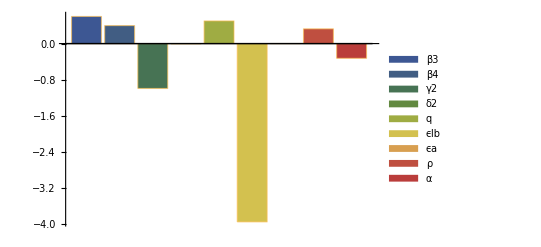

```mathematica
BarChart[{0.60123,0.39877,-0.9952,-0.0047144,0.50153,-3.95347,0.001162,0.3266,-0.3266},ChartLegends->{"β3","β4","γ2","δ2","q","ϵlb","ϵa","ρ","α"}, ChartStyle->"DarkRainbow"]
```

```mathematica
β3=0.3
β4=0.0495
δ2=0.00018256
γ2=0.037
q=0.2
ϵLB=0.87
ϵLB=0.87
ϵa=0.003545
α=0.00273
r=0.030421
S
```

0.3

0.0495

0.00018256

0.037

0.2

0.87

0.87

0.003545

0.00273

0.030421

0.00116203

```mathematica
β3=0.3
β4=0.0495
δ2=0.00018256
γ2=0.037
q=0.2
ϵLB=0.87
ϵLB=0.87
ϵa=0.003545
α=0.00273
r=0.030421
P
```

0.3

0.0495

0.00018256

0.037

0.2

0.87

0.87

0.003545

0.00273

0.030421

-0.326633

```mathematica
β3=0.3
β4=0.0495
δ2=0.00018256
γ2=0.037
q=0.2
ϵLB=0.87
ϵLB=0.87
ϵa=0.003545
α=0.00273
r=0.030421
M
```

0.3

0.0495

0.00018256

0.037

0.2

0.87

0.87

0.003545

0.00273

0.030421

0.326633